```mathematica
(*January 17, 2019*)
(*Calculating Pi Using Elastic Collisions*)
(*Louis R. Nemzer, Ph.D.*)

(*Based on the Video Posted by 3Blue1Brown*)
(* https://youtu.be/HEfHFsfGXjs *)
```

```mathematica
(*Using the Physics Formulas for Elastic Collisions, the velocities of the larger (m1=M) and smaller (m2=1) masses after each cycle of two collisions will by transformed using the matrix:*)
trans={{(M-1)/(M+1),-2/(M+1)},{2M/(M+1),-(-M+1)/(M+1)}};
MatrixForm[trans]
```

((-1+M)/(1+M) | -2/(1+M)
(2 M)/(1+M) | (-1+M)/(1+M))

```mathematica
(*Start with m1 moving with v = 1, and m2 stationary*)
start={{1},{0}};
```

```mathematica
Powers=Table[MatrixPower[trans,i].start,{i,0,50}];
Powers2=Partition[Flatten[Powers],2];
```

```mathematica
(*Cycle until m1 is completely turned around*)
C1=TakeWhile[(Powers2/.M->10^1),#[[2]]≥0&]; 
C2=TakeWhile[(Powers2/.M->10^2),#[[2]]≥0&];
C3=TakeWhile[(Powers2/.M->10^3),#[[2]]≥0&];
```

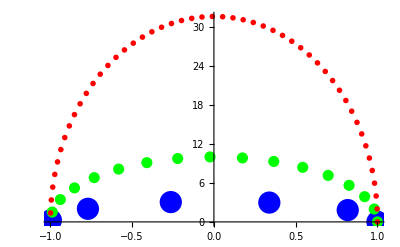

```mathematica
(*Plot phase space of v1 and v2*)
ListPlot[{C1,C2,C3},PlotRange->All,PlotStyle->{{PointSize[0.04],Blue},{PointSize[0.02],Green},{PointSize[0.01],Red}},PlotRange->All]
```

```mathematica
(* Conservation of energy requires (1/2)*M*(1)^2=(1/2)*M*v1^2+(1/2)*v2^2 -> v1^2+v2^2/M = 1, which is the equation of an ellipse with axes 1 and sqrt[M] *)
```

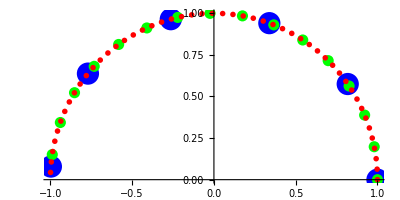

```mathematica
(*To get a circle, rescale y-axis by 1/sqrt[M]*)
squish = {{1,0},{0,1/Sqrt[M]}};
ListPlot[{Flatten[{squish.#} & /@ C1/.M->10^1,1],Flatten[{squish.#} & /@ C2/.M->10^2,1],Flatten[{squish.#} & /@ C3/.M->10^3,1]},PlotStyle->{{PointSize[0.04],Blue},{PointSize[0.02],Green},{PointSize[0.01],Red}},AspectRatio->Square]
```

```mathematica
(*Each pair of collisions advances the phase space by a fixed angle that depends on M:*) 
trans2=squish.trans;
MatrixForm[trans2]
```

((-1+M)/(1+M) | -2/(1+M)
(2 √M)/(1+M) | (-1+M)/(√M (1+M)))

```mathematica
angle=trans2.start
```

{{(-1+M)/(1+M)},{(2 √M)/(1+M)}}

```mathematica
angle2=ArcTan[angle[[2]]/angle[[1]]][[1]]
```

ArcTan[(2 √M)/(-1+M)]

```mathematica
Table[{100^i,2*Pi/angle2/.M->100^i,N[2*Pi/angle2/.M->100^i]},{i,1,5}];
MatrixForm[%]
```

(100 | (2 π)/ArcTan[20/99] | 31.5204
10000 | (2 π)/ArcTan[200/9999] | 314.17
1000000 | (2 π)/ArcTan[2000/999999] | 3141.59
100000000 | (2 π)/ArcTan[20000/99999999] | 31415.9
10000000000 | (2 π)/ArcTan[200000/9999999999] | 314159.)

```mathematica
(*Since ArcTan[x] = x - x^3/3..., ArcTan[(2*Sqrt[100^i])/(100^i-1)] approaches 2*10^-i. To go from 0 to Pi radians, it will take 10^i*Pi/2 cycles, or 10^i*Pi Collisions, accurate to i+1 digits.*)  
1
```

1